# HW10.3B Calculus

## Problem 1:

```mathematica
ClearAll["Global`*"]
```

```mathematica
r=2-Sin[θ];
```

```mathematica
(D[r,θ]*Sin[θ]+r*Cos[θ])/(D[r,θ]*Cos[θ]-r*Sin[θ])
```

```mathematica
F[θ_]:=(Cos[θ] (2-Sin[θ])-Cos[θ] Sin[θ])/(-Cos[θ]^2-(2-Sin[θ]) Sin[θ]);
```

```mathematica
F[π/3]
```

```mathematica
Simplify[(-(√3)/4+1/2 (2-(√3)/2))/(-1/4-1/2 √3 (2-(√3)/2))]
```

1/11 (4-3 √3)

## Problem 2:

```mathematica
(*Find the slope of the tangent line to the given polar curve at the point specified by the value of θ.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r = Cos[θ/3];
```

```mathematica
(D[r,θ]*Sin[θ]+r*Cos[θ])/(D[r,θ]*Cos[θ]-r*Sin[θ])
```

```mathematica
F[θ_]:=(Cos[θ/3] Cos[θ]-1/3 Sin[θ/3] Sin[θ])/(-1/3 Cos[θ] Sin[θ/3]-Cos[θ/3] Sin[θ]);
```

```mathematica
F[π]
```

-√3

## Problem 3:

```mathematica
(*Find the slope of the tangent line to the given polar curve at the point specified by the value of θ.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r=9+8*Cos[θ];
```

```mathematica
(D[r,θ]*Sin[θ]+r*Cos[θ])/(D[r,θ]*Cos[θ]-r*Sin[θ])
```

```mathematica
P[θ_]:=(Cos[θ] (9+8 Cos[θ])-8 Sin[θ]^2)/(-8 Cos[θ] Sin[θ]-(9+8 Cos[θ]) Sin[θ]);
```

```mathematica
P[π/3]
```

-1/(17 √3)

## Problem 4:

```mathematica
(*Find the points on the given curve where the tangent line is horizontal or vertical.; Do ordered pairs (r,θ)*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
0⩽θ⩽π;
```

```mathematica
r=3Cos[θ];
```

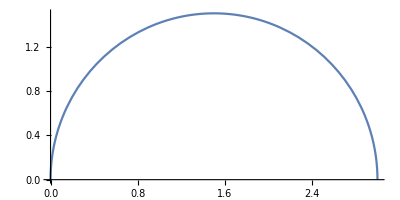

```mathematica
PolarPlot[r,{θ,0,π/2}]
```

```mathematica
3*Cos[π/2]
```

```mathematica
ArcCos[0]
```

π/2

```mathematica
(D[r,θ]*Sin[θ]+r*Cos[θ])/(D[r,θ]*Cos[θ]-r*Sin[θ])
```

```mathematica
K[θ_]:=-1/6 Csc[θ] Sec[θ] (3 Cos[θ]^2-3 Sin[θ]^2);
```

```mathematica
Solve[D[r,θ]*Sin[θ]+r*Cos[θ]==0,θ]
```

## Problem 5:

```mathematica
ClearAll["Global`*"]
```

```mathematica
r = 8*Sin[θ];
```

```mathematica
(D[r,θ]*Sin[θ]+r*Cos[θ])/(D[r,θ]*Cos[θ]-r*Sin[θ])
```

```mathematica
F[θ_]:=(16 Cos[θ] Sin[θ])/(8 Cos[θ]^2-8 Sin[θ]^2);
```

```mathematica
F[π/6]
```

√3

## Problem 6:

```mathematica
(*Find the slope of the tangent line to the given polar curve at the point specified by the value of θ.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r = Cos[2θ];
```

```mathematica
TrigReduce[(Sin[θ])^2-(Cos[θ])^2]
```

-Cos[2 θ]

```mathematica
ArcCos[π/2]
```

```mathematica
3*Cos[π/4]
```

3/(√2)

```mathematica
(D[r,θ]*Sin[θ]+r*Cos[θ])/(D[r,θ]*Cos[θ]-r*Sin[θ])
```

```mathematica
G[θ_]:=(Cos[θ] Cos[2 θ]-2 Sin[θ] Sin[2 θ])/(-Cos[2 θ] Sin[θ]-2 Cos[θ] Sin[2 θ]);
```

```mathematica
G[π/4]
```

```mathematica
TrigReduce[Sin[θ]*Cos[θ]]
```

1/2 Sin[2 θ]

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
Sqrt[(3/2)^2+(-3/2)^2]
```

3/(√2)